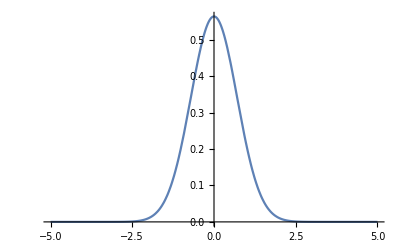

(ⅇ^(-(mw x^2)/(2 ℏ)) (mw/ℏ)^(1/4))/π^(1/4)

```mathematica
$Assumptions = {mw, t, ℏ, x} ∈ Reals && mw >0 && t >0 && ℏ > 0;
p0[x_] = Surd[mw/(π ℏ),4]Exp[-mw x^2 / (2 ℏ)];
Plot[Replace[Abs[p0[x]]^2, {mw -> 1, ℏ -> 1}, 7], {x, -5, 5}] 
p0[x]
```

```mathematica
aplus[f_] := (1/Sqrt[2 ℏ mw])(-ℏ D[f, x] + mw x f)
p1[x_]=aplus[p0[x]] // Simplify
```

(√2 ⅇ^(-(mw x^2)/(2 ℏ)) x (mw/ℏ)^(3/4))/π^(1/4)

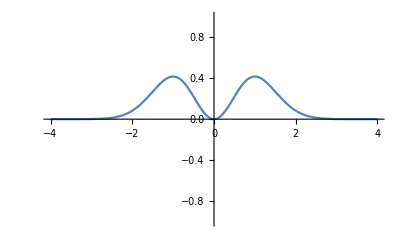

```mathematica
Plot[Replace[Abs[p1[x]]^2, {mw -> 1, ℏ -> 1}, 7],{x,-4,4}, PlotRange -> {-1, 1}]
```

```mathematica
Integrate[Abs[p1[x]]^2, {x, -∞, ∞}]
```

1

```mathematica
basestate = p0[x]
p[x_, n_] := (1/Sqrt[Factorial[n]])Nest[aplus,basestate, n]
```

(ⅇ^(-(mw x^2)/(2 ℏ)) (mw/ℏ)^(1/4))/π^(1/4)

(ⅇ^(-(mw x^2)/(2 ℏ)) mw^(1/4) (2 mw x^2-ℏ))/(√2 π^(1/4) ℏ^(5/4))

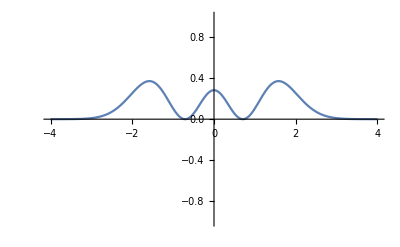

```mathematica
p2[x_] = p[x, 2] // FullSimplify
Plot[Replace[Abs[p2[x]]^2, {mw -> 1, ℏ -> 1}, 7],{x,-4,4}, PlotRange -> {-1, 1}]
```

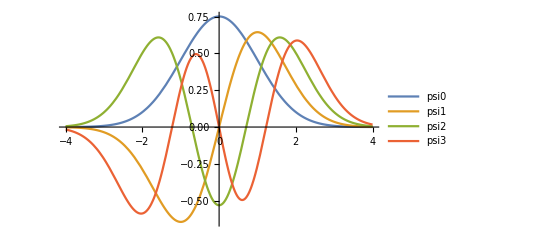

```mathematica
plt = Plot[Evaluate@Table[Replace[p[x, n] //FullSimplify, {mw -> 1, ℏ -> 1}, 20], {n, 0, 3}], {x, -4, 4}, PlotLegends -> {"psi0", "psi1", "psi2", "psi3", "psi4"}]
```

```mathematica
Rasterize[plt, ImageResolution -> 700]
```

-Graphics-

```mathematica
(* Checking orthogonality *)
Integrate[p[x, 1]p[x, 2], {x, -∞, ∞}] 
Integrate[p[x, 1]p[x, 1], {x, -∞, ∞}]
```

0

1

```mathematica
(* Expected value on p1, p2 *)
Integrate[p0[x] x p0[x], {x, -∞, ∞}]
Integrate[p1[x] x p1[x], {x, -∞, ∞}]
Integrate[p0[x] x^2 p0[x], {x, -∞, ∞}]
Integrate[p1[x] x^2 p1[x], {x, -∞, ∞}]
```

0

0

ℏ/(2 mw)

(3 ℏ)/(2 mw)

```mathematica
pop[f_, x_] := -ⅈ ℏ D[f, x]
Integrate[p0[x]pop[p0[x], x], {x, -∞, ∞}]
Integrate[p1[x]pop[p1[x], x], {x, -∞, ∞}]
Integrate[p0[x]pop[pop[p0[x], x], x], {x, -∞, ∞}]
Integrate[p1[x]pop[pop[p1[x], x], x], {x, -∞, ∞}]
```

0

0

(mw ℏ)/2

(3 mw ℏ)/2

ℏ/(2 mw)

(3 ℏ)/(2 mw)